```mathematica
Manipulate[
Module[{choose1,choose2,P2,v1,v2,h1,h2,Pf,Pb1,Pb2,sb,pb1,pb2,Pt1,Pt2,st,pt1,pt2,wb,wt,p1,p2},
choose1[c1_,c2_,c3_,c4_]=Which[pick1==1,c1,pick1==2,c2,pick1==3,c3,pick1==4,c4];
choose2[c1_,c2_,c3_,c4_]=Which[pick2==1,c1,pick2==2,c2,pick2==3,c3,pick2==4,c4];

P2=If[bn==1,Pf1,Pf2];

v1=0.9;v2=0.9;
h1[v_]=0.1+0.8;
h2[v_]=h1[v]+0.075;

Pf=P2;

Pb1=If[bn==1,0.9,0];Pb2=If[bn==1,1.5,0.6];
sb=Quiet@Solve[
0==(Pb1-pmin1)/(pmax1-pmin1)&&1==(Pb2-pmin1)/(pmax1-pmin1),{pmin1,pmax1}];
pb1=pmin1/.sb[[1]];
pb2=pmax1/.sb[[1]];

Pt1=If[bn==1,1.5,0.6];Pt2=If[bn==1,2,1.1];
st=Quiet@Solve[
0==(Pt1-pmin2)/(pmax2-pmin2)&&1==(Pt2-pmin2)/(pmax2-pmin2),{pmin2,pmax2}];
pt1=pmin2/.st[[1]];
pt2=pmax2/.st[[1]];

wb=If[Pf≤Pb2,(Pf-pb1)/(pb2-pb1),1];
wt=(Pf-pt1)/(pt2-pt1);

p1=Graphics[{
{Opacity[0.7,RGBColor[0.16,1.,0.36]],Rectangle[{0,0},{0.7,h1[v1]}],Rectangle[{1.25,0},{1.95,h1[v2]}]},
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,h1[v1]},{0.7,h2[v1]}],Rectangle[{1.25,h1[v2]},{1.95,h2[v2]}]},
{Thickness[0.005],Line[{{0,1.1},{0,0},{0.7,0},{0.7,1.1}}],Line[{{1.25,1.1},{1.25,0},{1.95,0},{1.95,1.1}}]},

{EdgeForm[Black],If[bn==1,RGBColor[0.,0.19,0.52],RGBColor[0.,0.72,0.67]],
Table[Rectangle[{n*0.0125+(n-1)*0.05,h2[v1]},{n*0.0625,h2[v1]+0.055}],{n,1,11*wb}],
Table[Rectangle[{0.03125+n*0.0125+(n-1)*0.05,h2[v1]+0.055},{0.03125+n*0.0625,h2[v1]+2*0.055}],{n,1,10*wt}],
Table[Rectangle[{1.25+n*0.0125+(n-1)*0.05,h2[v2]},{1.25+n*0.0625,h2[v2]+0.055}],{n,1,11*wb}],
Table[Rectangle[{1.25+0.03125+n*0.0125+(n-1)*0.05,h2[v2]+0.055},{1.25+0.03125+n*0.0625,h2[v2]+2*0.055}],{n,1,10*wt}]},

Text[Style[Column[{wb,wt}],16],{1,1.25}],

Text[Framed[Style[choose1["reversible isothermal","reversible adiabatic","irreversible isothermal","irreversible adiabatic"],18],FrameMargins->{choose1[{9,9.5},{14,15},{4.5,4.5},{10,10}],{5,5}}],{0.35,1.45}],
Text[Framed[Style[choose2["reversible isothermal","reversible adiabatic","irreversible isothermal","irreversible adiabatic"],18],FrameMargins->{choose2[{9,9.5},{14,15},{4.5,4.5},{10,10}],{5,5}}],{1.6,1.45}]
},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{0,1.65}}];

p2=Graphics[Text[Style[Row[{Column[{"bottom",Grid[{{"min =",pb1},{"max =",pb2}}]},Center],Spacer[30],Column[{"top",Grid[{{"min =",pt1},{"max =",pt2}}]},Center]}],16]]];
Show[Switch[omm,1,p1,2,p2]]
],
Control[{{omm,1,""},{1->" p1 ",2->" p2 "},Setter}],
Control[{{bn,1,""},{1->"compression",2->"expansion"},Setter}],
Style["choose two conditions:",Bold],
Row[{
Control[{{pick1,2,""},{1->"reversible isothermal",2->"reversible adiabatic",3->"irreversible isothermal",4->"irreversible adiabatic"},PopupMenu}],
Control[{{pick2,4,""},{1->"reversible isothermal",2->"reversible adiabatic",3->"irreversible isothermal",4->"irreversible adiabatic"},PopupMenu}]}],
PaneSelector[{
1->Control[{{Pf1,1.5,"final pressure (MPa)"},1,2,0.1,Appearance->"Labeled"}],
2->Control[{{Pf2,0.6,"final pressure (MPa)"},0.1,1.1,0.1,Appearance->"Labeled"}]
},Dynamic@bn]]
```

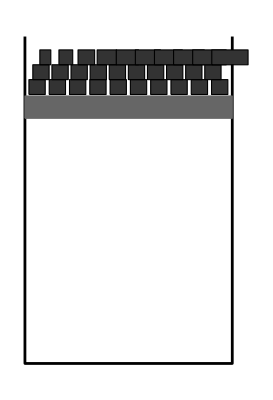

```mathematica
Module[{L,δ1,δ2,δ3,h},
L=0.055;
δ1=0.0135;
δ2=0.0095;
δ3=0.0095;
h=0.05;
Graphics[{
{Thickness[0.005],Line[{{0,1.1},{0,0},{0.7,0},{0.7,1.1}}]},
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,0.9},{0.7,0.9-0.075}]},
{EdgeForm[Black],GrayLevel[0.2],
Table[Rectangle[{n*δ1+(n-1)*L,0.905},{n*(δ1+L),0.905+h}],{n,1,10}],
Table[Rectangle[{0.25*(δ1+L)+n*δ2+(n-1)*L,0.905+h},{0.25*(δ1+L)+n*(δ2+L),0.905+2*h}],{n,1,10}],
Table[Rectangle[{0.5*(0.25*(δ1+L)+δ2+L)+n*δ3+(n-1)*L,0.905+2*h},{0.5*(0.25*(δ1+L)+δ2)+n*(δ3+δ2+L),0.905+3*h}],{n,1,10}]
(*Table[Rectangle[{(0.25*(δ1+L)+(δ1+L))+(n-1)*δ3+(n-1)*L,0.905+2*h},{0.25*(δ1+L)+n*(δ2+L),0.905+3*h}],{n,1,10}]*)
}
}]
]
```

```mathematica
list1=Table[a,{a,1.1,2,0.1}];
list2=Table[b,{b,0.1,1,0.1}];
Length[list1]
Length[list2]
```

10

10

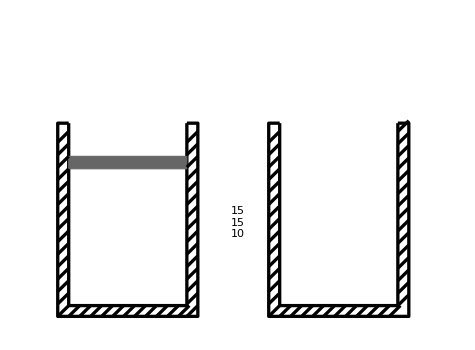

```mathematica
Module[{δ},
δ=0.065;
Graphics[{
{Thickness[0.005],Line[{{0,1.1},{0,0},{0.7,0},{0.7,1.1}}],Line[{{1.25,1.1},{1.25,0},{1.95,0},{1.95,1.1}}]},
{EdgeForm[Thick],GrayLevel[0.4],Rectangle[{0,0.9},{0.7,0.9-0.075}]},
{Thickness[0.005],
Line[{{0,1.1},{-δ,1.1},{-δ,-δ},{0.7+δ,-δ},{0.7+δ,1.1},{0.7,1.1}}],
(*Table[Line[{{-δ,-δ+i},{0,i}}],{i,0,1.1,0.075}],
Table[Line[{{i,-δ},{i+δ,0}}],{i,0,0.7,δ}],
Table[Line[{{0.7,-δ+i},{0.7+δ,i}}],{i,0,1.1,0.075}]*)
Table[Line[{{-δ,-δ+i},{0,i}}],{i,0,1.1,0.075}],
Table[Line[{{i,-δ},{i+δ,0}}],{i,0,0.7,δ}],
Table[Line[{{0.7,-δ+i},{0.7+δ,i}}],{i,0,1.1,0.075}],

Line[{{1.25,1.1},{1.25-δ,1.1},{1.25-δ,-δ},{1.95+δ,-δ},{1.95+δ,1.1},{1.95,1.1}}],
Table[Line[{{1.25-δ,-δ+i},{1.25,i}}],{i,0,1.1,0.075}],
Table[Line[{{1.25-δ+n*δ,-δ},{1.25+n*δ,0}}],{n,1,11}],
Table[Line[{{1.95,i},{1.95+δ,i+δ}}],{i,0,1.1,0.075}]
},
Text[Column[{
Length[Table[Line[{{1.25-δ,-δ+i},{1.25,i}}],{i,0,1.1,0.075}]],
Length[Table[Line[{{1.95,-δ+i},{1.95+δ,i}}],{i,0,1.1,0.075}]],
Length[Table[Line[{{1.25-δ+n*δ,-δ},{1.25+n*δ,0}}],{n,1,10}]]
}],{1,0.5}]
},ImageSize->{475,350},PlotRange->{{-0.15,2.15},{-δ-0.01,1.65}}]
]
```